# QED calculation: Peskin Sec. 5

## e^-μ^-→e^-μ^- (QED): Peskin P.153-54

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (12 Mar 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

### Create Topology

```mathematica
topologies=CreateTopologies[0,2->2];
(*Paint[topologies];*)
```

### Insert Particles

Appendix B of the FeynArts manual contains a list of the particles in the (default) SM model.

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes}];
```

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 4 Classes insertions

> Top. 4: 0 Classes insertions

in total: 4 Classes insertions

> Top. 1 aebf/cedf/ef.m, 4 diagrams

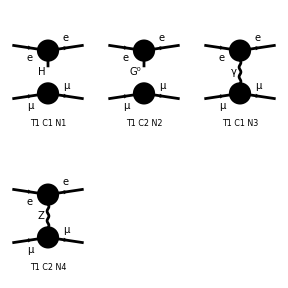

```mathematica
Paint[diagrams];
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebf/cedf/ef.m, 1 diagram

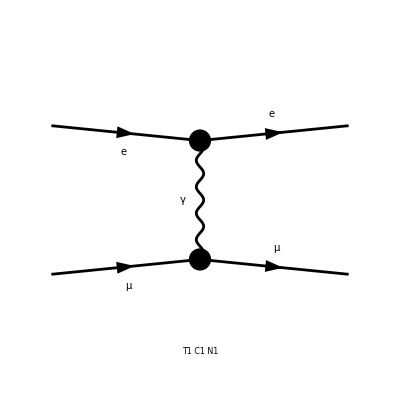

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}}}→{{F[2,{1}],k[3],ME,{-Charge,LeptonNumber}},{F[2,{2}],k[4],MM,{-Charge,LeptonNumber}}}][4 Alfa π Den[T,0] Mat[F1]-2 Alfa π Den[T,0] Mat[F2]-4 Alfa π Den[T,0] Mat[F3]+2 Alfa π Den[T,0] Mat[F4]]

Remember that SquaredME returns a list of {squared, squaredRules}.
In Lecture 1-1 we applied the rules right now to avoid confusion.
Here we follow the official recommendation: applying the rules as late as possible to improve the calculation speed.

```mathematica
squared=SquaredME[amplitude]
```

{FF[F1] (FFC[F1] Mat[F1,F1]+FFC[F2] Mat[F1,F2]+FFC[F3] Mat[F1,F3]+FFC[F4] Mat[F1,F4])+FF[F2] (FFC[F1] Mat[F2,F1]+FFC[F2] Mat[F2,F2]+FFC[F3] Mat[F2,F3]+FFC[F4] Mat[F2,F4])+FF[F3] (FFC[F1] Mat[F3,F1]+FFC[F2] Mat[F3,F2]+FFC[F3] Mat[F3,F3]+FFC[F4] Mat[F3,F4])+FF[F4] (FFC[F1] Mat[F4,F1]+FFC[F2] Mat[F4,F2]+FFC[F3] Mat[F4,F3]+FFC[F4] Mat[F4,F4]),{FF[F1]→4 Alfa π Den[T,0],FF[F2]→-2 Alfa π Den[T,0],FF[F3]→-4 Alfa π Den[T,0],FF[F4]→2 Alfa π Den[T,0],FFC[F1]→4 Alfa π Den[T,0],FFC[F2]→-2 Alfa π Den[T,0],FFC[F3]→-4 Alfa π Den[T,0],FFC[F4]→2 Alfa π Den[T,0]}}

```mathematica
helSquared=squared//.HelicityME[amplitude]
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

{FF[F4] (FFC[F1] (1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U))-1/2 (Abb16 ME2-2 Abb14 ME MM+Abb15 MM2) Hel[1] Hel[2]+(ME+MM) (Eps3 Hel[1]+Eps11 Hel[2])+(Eps4 (ME+MM)-(Abb18 ME-Abb17 MM) Hel[1] Hel[2]+1/4 (Abb27 Hel[1]+Abb32 Hel[2])) Hel[3]+(Eps7 (ME+MM)-(Abb23 ME-Abb21 MM) Hel[1] Hel[2]+1/4 (Abb28 Hel[1]+Abb30 Hel[2])+(1/2 (-Abb34 ME2+2 Abb35 ME MM-Abb31 MM2)-(Abb33 ME+Abb25 MM) Hel[1]-(Abb29 ME+Abb26 MM) Hel[2]-1/2 (Abb20 ME2-2 Abb24 ME MM+Abb19 MM2) Hel[1] Hel[2]) Hel[3]) Hel[4])+FFC[F4] (1/2 (ME2^2+14 ME2 MM2+MM2^2-4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U))+(Abb115 ME2+2 Abb114 ME MM+Abb113 MM2) Hel[2] Hel[3]+Hel[1] ((Abb105-2 (Abb102 ME MM+ME2 MM2 Pair1)) Hel[2]+(Abb118 ME2+2 Abb106 ME MM+Abb75 MM2) Hel[3])+((Abb112 ME2+2 Abb111 ME MM+Abb110 MM2) Hel[1]+(Abb99 ME2+2 Abb117 ME MM+Abb116 MM2) Hel[2]+(Abb121-2 (Abb119 ME MM+ME2 MM2 Pair4)+1/2 (Abb125-4 Abb109 ME MM+4 Abb103 ME2 MM2) Hel[1] Hel[2]) Hel[3]) Hel[4])+FFC[F3] ((1/4 (Abb54+4 (Abb47 ME MM+ME2 MM2 Pair18)) Hel[1]+(1/4 (-Abb64-4 (Abb56 ME MM+ME2 MM2 Pair15))-1/2 ((Abb42+2 Eps16 ME2) MM+ME (Abb36+2 Eps15 MM2)) Hel[1]) Hel[2]) Hel[3]+(-1/4 (Abb60+4 (Abb52 ME MM+ME2 MM2 Pair16)) Hel[1]+(1/4 (Abb66+4 (Abb62 ME MM+ME2 MM2 Pair17))+1/2 ((Abb45+2 Eps21 ME2) MM+ME (Abb50+2 Eps19 MM2)) Hel[1]) Hel[2]+(1/2 ((Abb48+2 Eps24 ME2) MM+ME (Abb49+2 Eps22 MM2)) Hel[1]-1/2 ((Abb58+2 Eps27 ME2) MM+ME (Abb57+2 Eps29 MM2)+(Abb44 ME2-2 Abb43 ME MM+Abb40 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F2] (1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U))-2 (Eps3 MM Hel[1]+Eps11 ME Hel[2])-((Abb76 ME2-Abb75 MM2) Hel[1]+(2 Abb89 ME MM-1/2 (Abb72 ME+Abb69 MM+4 Eps31 ME MM2) Hel[1]) Hel[2]) Hel[3]-MM (-2 Abb67 ME Hel[1] Hel[2]+2 Eps4 Hel[3])-(2 ME (Eps7+Abb87 MM Hel[1])+(-Abb99 ME2+Abb97 MM2-1/2 (Abb74 ME+(Abb82-4 Eps32 ME2) MM) Hel[1]) Hel[2]+(2 Abb100 ME MM-1/2 (Abb80 ME-Abb81 MM-4 Eps33 ME MM2) Hel[1]+1/2 (Abb101 ME-(Abb96+4 Eps34 ME2) MM+(Abb94-4 Abb71 ME2 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4]))+FF[F3] (1/4 FFC[F3] (4 ME2 MM2-4 ME MM (ME2+MM2-S)+(ME2+MM2-S)^2-(Abb3-4 (Abb1 ME MM+ME2 MM2 Pair1)) Hel[1] Hel[2]-(Abb6-4 (Abb4 ME MM+ME2 MM2 Pair4)) Hel[3] Hel[4]+(Abb5+4 (Abb2 ME MM+ME2 MM2 Pair1 Pair4)) Hel[1] Hel[2] Hel[3] Hel[4])+FFC[F2] ((ME-MM) (-Eps3 Hel[1]+Eps11 Hel[2])+1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)+(Abb16 ME2+2 Abb14 ME MM+Abb15 MM2) Hel[1] Hel[2])+(-Eps4 (ME-MM)+1/4 Abb27 Hel[1]+(-Abb32/4-(Abb18 ME+Abb17 MM) Hel[1]) Hel[2]) Hel[3]+(Eps7 (ME-MM)-1/4 Abb28 Hel[1]+(Abb30/4+(Abb23 ME+Abb21 MM) Hel[1]) Hel[2]+(1/2 (Abb34 ME2+2 Abb35 ME MM+Abb31 MM2)-(Abb33 ME-Abb25 MM) Hel[1]+(Abb29 ME-Abb26 MM-1/2 (Abb20 ME2+2 Abb24 ME MM+Abb19 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F4] ((1/4 (Abb54+4 (Abb47 ME MM+ME2 MM2 Pair18)) Hel[1]+(1/4 (-Abb64-4 (Abb56 ME MM+ME2 MM2 Pair15))+1/2 ((Abb42+2 Eps16 ME2) MM+ME (Abb36+2 Eps15 MM2)) Hel[1]) Hel[2]) Hel[3]+(-1/4 (Abb60+4 (Abb52 ME MM+ME2 MM2 Pair16)) Hel[1]+(1/4 (Abb66+4 (Abb62 ME MM+ME2 MM2 Pair17))-1/2 ((Abb45+2 Eps21 ME2) MM+ME (Abb50+2 Eps19 MM2)) Hel[1]) Hel[2]+(-1/2 ((Abb48+2 Eps24 ME2) MM+ME (Abb49+2 Eps22 MM2)) Hel[1]+(1/2 ((Abb58+2 Eps27 ME2) MM+ME (Abb57+2 Eps29 MM2))-1/2 (Abb44 ME2-2 Abb43 ME MM+Abb40 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F1] (-Pair5 (ME2 Pair2 Hel[1]+ME (MM Pair3-Eps1 Hel[1]) Hel[2]) Hel[3]-(Pair6 (ME MM Pair2 Hel[1]+(MM2 Pair3-Eps1 MM Hel[1]) Hel[2])+(-1/4 Abb12 Hel[1] Hel[2]+Eps2 (ME Pair2 Hel[1]+MM Pair3 Hel[2])) Hel[3]) Hel[4]))+FF[F1] (1/4 FFC[F1] (4 (ME2 MM2+ME MM (ME2+MM2-S))+(ME2+MM2-S)^2+(Abb3+4 Abb1 ME MM-4 ME2 MM2 Pair1) Hel[1] Hel[2]+(Abb6+4 Abb4 ME MM-4 ME2 MM2 Pair4+(Abb5-4 Abb2 ME MM+4 ME2 MM2 Pair1 Pair4) Hel[1] Hel[2]) Hel[3] Hel[4])+FFC[F4] (1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U))-1/2 (Abb16 ME2-2 Abb14 ME MM+Abb15 MM2) Hel[1] Hel[2]-(ME+MM) (Eps3 Hel[1]+Eps11 Hel[2])+(-Eps4 (ME+MM)+(Abb18 ME-Abb17 MM) Hel[1] Hel[2]+1/4 (Abb27 Hel[1]+Abb32 Hel[2])) Hel[3]+(-Eps7 (ME+MM)+(Abb23 ME-Abb21 MM) Hel[1] Hel[2]+1/4 (Abb28 Hel[1]+Abb30 Hel[2])+(1/2 (-Abb34 ME2+2 Abb35 ME MM-Abb31 MM2)+(Abb33 ME+Abb25 MM) Hel[1]+(Abb29 ME+Abb26 MM-1/2 (Abb20 ME2-2 Abb24 ME MM+Abb19 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F3] (-Pair5 (ME2 Pair2 Hel[1]+ME (MM Pair3+Eps1 Hel[1]) Hel[2]) Hel[3]-(Pair6 (ME MM Pair2 Hel[1]+(MM2 Pair3+Eps1 MM Hel[1]) Hel[2])+(-1/4 Abb12 Hel[1] Hel[2]-Eps2 (ME Pair2 Hel[1]+MM Pair3 Hel[2])) Hel[3]) Hel[4])+FFC[F2] (1/4 ((Abb54-4 Abb47 ME MM+4 ME2 MM2 Pair18) Hel[1]+(Abb64-4 Abb56 ME MM+4 ME2 MM2 Pair15) Hel[2]) Hel[3]+((1/4 (Abb66-4 Abb62 ME MM+4 ME2 MM2 Pair17)-1/2 ((-Abb45-2 Eps21 ME2) MM+ME (Abb50+2 Eps19 MM2)) Hel[1]) Hel[2]+(-1/2 (Abb44 ME2+2 Abb43 ME MM+Abb40 MM2) Hel[1] Hel[2]+1/2 (((-Abb48-2 Eps24 ME2) MM+ME (Abb49+2 Eps22 MM2)) Hel[1]+((-Abb58-2 Eps27 ME2) MM+ME (Abb57+2 Eps29 MM2)) Hel[2])) Hel[3]) Hel[4]+Hel[1] (-1/2 ((-Abb42-2 Eps16 ME2) MM+ME (Abb36+2 Eps15 MM2)) Hel[2] Hel[3]+1/4 (Abb60-4 Abb52 ME MM+4 ME2 MM2 Pair16) Hel[4])))+FF[F2] (FFC[F2] (1/2 (ME2^2+14 ME2 MM2+MM2^2+4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U))-(Abb115 ME2-2 Abb114 ME MM+Abb113 MM2) Hel[2] Hel[3]+Hel[1] (-(Abb105+2 Abb102 ME MM-2 ME2 MM2 Pair1) Hel[2]+(Abb118 ME2-2 Abb106 ME MM+Abb75 MM2) Hel[3])-(Abb112 ME2-2 Abb111 ME MM+Abb110 MM2) Hel[1] Hel[4]+((Abb99 ME2-2 Abb117 ME MM+Abb116 MM2) Hel[2]+(-Abb121-2 Abb119 ME MM+2 ME2 MM2 Pair4+1/2 (Abb125+4 (Abb109 ME MM+Abb103 ME2 MM2)) Hel[1] Hel[2]) Hel[3]) Hel[4])+FFC[F3] ((ME-MM) (Eps3 Hel[1]-Eps11 Hel[2])+1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)+(Abb16 ME2+2 Abb14 ME MM+Abb15 MM2) Hel[1] Hel[2])+(Eps4 (ME-MM)+1/4 Abb27 Hel[1]+(-Abb32/4+(Abb18 ME+Abb17 MM) Hel[1]) Hel[2]) Hel[3]+(-Eps7 (ME-MM)-1/4 Abb28 Hel[1]+(Abb30/4-(Abb23 ME+Abb21 MM) Hel[1]) Hel[2]+(1/2 (Abb34 ME2+2 Abb35 ME MM+Abb31 MM2)+(Abb33 ME-Abb25 MM) Hel[1]+(-Abb29 ME+Abb26 MM-1/2 (Abb20 ME2+2 Abb24 ME MM+Abb19 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F4] (1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U))-((Abb76 ME2-Abb75 MM2) Hel[1]+(2 Abb89 ME MM+1/2 (Abb72 ME-Abb69 MM+4 Eps31 ME MM2) Hel[1]) Hel[2]) Hel[3]+2 (Eps3 MM Hel[1]+ME (Eps11+Abb67 MM Hel[1]) Hel[2]+Eps4 MM Hel[3])-(ME (-2 Eps7+2 Abb87 MM Hel[1])+(-Abb99 ME2+Abb97 MM2-1/2 (Abb74 ME-(Abb82-4 Eps32 ME2) MM) Hel[1]) Hel[2]+(2 Abb100 ME MM+1/2 ((Abb80 ME+Abb81 MM-4 Eps33 ME MM2) Hel[1]+(Abb101 ME+(Abb96+4 Eps34 ME2) MM+(Abb94-4 Abb71 ME2 MM2) Hel[1]) Hel[2])) Hel[3]) Hel[4])+FFC[F1] (1/4 ((Abb54-4 Abb47 ME MM+4 ME2 MM2 Pair18) Hel[1]+(Abb64-4 Abb56 ME MM+4 ME2 MM2 Pair15) Hel[2]) Hel[3]+((1/4 (Abb66-4 Abb62 ME MM+4 ME2 MM2 Pair17)+1/2 ((-Abb45-2 Eps21 ME2) MM+ME (Abb50+2 Eps19 MM2)) Hel[1]) Hel[2]-1/2 (((-Abb48-2 Eps24 ME2) MM+ME (Abb49+2 Eps22 MM2)) Hel[1]+((-Abb58-2 Eps27 ME2) MM+ME (Abb57+2 Eps29 MM2)+(Abb44 ME2+2 Abb43 ME MM+Abb40 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4]+Hel[1] (1/2 ((-Abb42-2 Eps16 ME2) MM+ME (Abb36+2 Eps15 MM2)) Hel[2] Hel[3]+1/4 (Abb60-4 Abb52 ME MM+4 ME2 MM2 Pair16) Hel[4]))),{FF[F1]→4 Alfa π Den[T,0],FF[F2]→-2 Alfa π Den[T,0],FF[F3]→-4 Alfa π Den[T,0],FF[F4]→2 Alfa π Den[T,0],FFC[F1]→4 Alfa π Den[T,0],FFC[F2]→-2 Alfa π Den[T,0],FFC[F3]→-4 Alfa π Den[T,0],FFC[F4]→2 Alfa π Den[T,0]}}

```mathematica
matrixElement=helSquared//.{Hel[_]->0}
```

{FF[F3] (1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)) FFC[F2]+1/4 (4 ME2 MM2-4 ME MM (ME2+MM2-S)+(ME2+MM2-S)^2) FFC[F3])+FF[F2] (1/2 (ME2^2+14 ME2 MM2+MM2^2+4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U)) FFC[F2]+1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)) FFC[F3]+1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U)) FFC[F4])+FF[F1] (1/4 (4 (ME2 MM2+ME MM (ME2+MM2-S))+(ME2+MM2-S)^2) FFC[F1]+1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U)) FFC[F4])+FF[F4] (1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U)) FFC[F1]+1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U)) FFC[F2]+1/2 (ME2^2+14 ME2 MM2+MM2^2-4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U)) FFC[F4]),{FF[F1]→4 Alfa π Den[T,0],FF[F2]→-2 Alfa π Den[T,0],FF[F3]→-4 Alfa π Den[T,0],FF[F4]→2 Alfa π Den[T,0],FFC[F1]→4 Alfa π Den[T,0],FFC[F2]→-2 Alfa π Den[T,0],FFC[F3]→-4 Alfa π Den[T,0],FFC[F4]→2 Alfa π Den[T,0]}}

We have obtained unpolarized amplitude by Hel[_]→0. Instead, setting _Hel=0 in advance gives the same result (and actually faster).

```mathematica
_Hel=0;
squared = SquaredME[amplitude] 
helAveragedSquared=squared//.HelicityME[amplitude]//Simplify
```

{FF[F1] (FFC[F1] Mat[F1,F1]+FFC[F2] Mat[F1,F2]+FFC[F3] Mat[F1,F3]+FFC[F4] Mat[F1,F4])+FF[F2] (FFC[F1] Mat[F2,F1]+FFC[F2] Mat[F2,F2]+FFC[F3] Mat[F2,F3]+FFC[F4] Mat[F2,F4])+FF[F3] (FFC[F1] Mat[F3,F1]+FFC[F2] Mat[F3,F2]+FFC[F3] Mat[F3,F3]+FFC[F4] Mat[F3,F4])+FF[F4] (FFC[F1] Mat[F4,F1]+FFC[F2] Mat[F4,F2]+FFC[F3] Mat[F4,F3]+FFC[F4] Mat[F4,F4]),{FF[F1]→4 Alfa π Den[T,0],FF[F2]→-2 Alfa π Den[T,0],FF[F3]→-4 Alfa π Den[T,0],FF[F4]→2 Alfa π Den[T,0],FFC[F1]→4 Alfa π Den[T,0],FFC[F2]→-2 Alfa π Den[T,0],FFC[F3]→-4 Alfa π Den[T,0],FFC[F4]→2 Alfa π Den[T,0]}}

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

{1/4 (FF[F3] (2 (MM2 T+ME2 (-4 MM2+T)-2 ME MM (ME2+MM2-U)) FFC[F2]+(4 ME2 MM2-4 ME MM (ME2+MM2-S)+(ME2+MM2-S)^2) FFC[F3])+FF[F1] ((4 ME2 MM2+4 ME MM (ME2+MM2-S)+(ME2+MM2-S)^2) FFC[F1]+2 (MM2 T+ME2 (-4 MM2+T)+2 ME MM (ME2+MM2-U)) FFC[F4])+2 FF[F4] ((MM2 T+ME2 (-4 MM2+T)+2 ME MM (ME2+MM2-U)) FFC[F1]-(ME2^2+MM2^2-2 ME2 (MM2-S)+2 MM2 S-S (S+2 U)) FFC[F2]+(ME2^2+MM2^2+4 ME MM (-MM2+S)-2 MM2 T+T^2-2 MM2 U+U^2-2 ME2 (2 ME MM-7 MM2+T+U)) FFC[F4])+2 FF[F2] ((ME2^2+MM2^2+4 ME MM (MM2-S)-2 MM2 T+T^2+2 ME2 (2 ME MM+7 MM2-T-U)-2 MM2 U+U^2) FFC[F2]+(MM2 T+ME2 (-4 MM2+T)-2 ME MM (ME2+MM2-U)) FFC[F3]-(ME2^2+MM2^2-2 ME2 (MM2-S)+2 MM2 S-S (S+2 U)) FFC[F4])),{FF[F1]→4 Alfa π Den[T,0],FF[F2]→-2 Alfa π Den[T,0],FF[F3]→-4 Alfa π Den[T,0],FF[F4]→2 Alfa π Den[T,0],FFC[F1]→4 Alfa π Den[T,0],FFC[F2]→-2 Alfa π Den[T,0],FFC[F3]→-4 Alfa π Den[T,0],FFC[F4]→2 Alfa π Den[T,0]}}

This is not the result. We should

multiply it by four (Do you remember why?), and

apply the second part (we above called “squaredRules” ) to the first part.

So,

```mathematica
result=4*(helAveragedSquared[[1]]//.helAveragedSquared[[2]])//Simplify
```

16 Alfa2 π^2 (4 ME2^2+4 MM2^2+S^2+T^2+2 ME2 (4 MM2-S+T-U)-2 S U+U^2-2 MM2 (S-T+U)) Den[T,0]^2

```mathematica
ourResult=result//.{ME->0,ME2->0,Den[a_,b_]:>(a-b)^(-1),S->(kk+EE)^2,T->-2 kk^2(1-CosTheta),U->2ME2+2MM2-S-T}
```

(4 Alfa2 (4 (1-CosTheta)^2 kk^4+(EE+kk)^4+4 MM2^2-2 MM2 (4 (1-CosTheta) kk^2+2 MM2)-2 (EE+kk)^2 (2 (1-CosTheta) kk^2-(EE+kk)^2+2 MM2)+(2 (1-CosTheta) kk^2-(EE+kk)^2+2 MM2)^2) π^2)/((1-CosTheta)^2 kk^4)

```mathematica
PeskinResult=(2(4π Alfa)^2)/(kk^2(1-CosTheta)^2)((EE+kk)^2+(EE+kk CosTheta)^2-MM2(1-CosTheta))
FullSimplify[ourResult==PeskinResult,Assumptions->EE^2==kk^2+MM2]
```

(32 Alfa2 ((EE+kk)^2+(EE+CosTheta kk)^2-(1-CosTheta) MM2) π^2)/((1-CosTheta)^2 kk^2)

True

OK.
Now let us review the procedure:

```mathematica
topologies=CreateTopologies[0,2->2];
diagrams=InsertFields[topologies,{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[diagrams];
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebf/cedf/ef.m, 1 diagram

-Graphics-

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA];
_Hel=0;
helSquared=SquaredME[amplitude]//.HelicityME[amplitude];
result=4*helSquared[[1]]//.helSquared[[2]]//Simplify
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

16 Alfa2 π^2 (4 ME2^2+4 MM2^2+S^2+T^2+2 ME2 (4 MM2-S+T-U)-2 S U+U^2-2 MM2 (S-T+U)) Den[T,0]^2

```mathematica
result//.{ME->0,ME2->0,Den[a_,b_]:>(a-b)^(-1),S->(kk+EE)^2,T->-2 kk^2(1-CosTheta),U->2ME2+2MM2-S-T}
FullSimplify[%==PeskinResult,Assumptions->EE^2==kk^2+MM2]
```

(4 Alfa2 (4 (1-CosTheta)^2 kk^4+(EE+kk)^4+4 MM2^2-2 MM2 (4 (1-CosTheta) kk^2+2 MM2)-2 (EE+kk)^2 (2 (1-CosTheta) kk^2-(EE+kk)^2+2 MM2)+(2 (1-CosTheta) kk^2-(EE+kk)^2+2 MM2)^2) π^2)/((1-CosTheta)^2 kk^4)

True